```mathematica
ClearAll["Global`*"]
```

```mathematica
M2[n_,k_] := M2[n,k] = Sum[ MoebiusMu[j]M2[Floor[n/j],k-1],{j,2,n}];M2[n_,0]:=1
M1[n_,z_]:=Sum[FactorialPower[z,a]/a! M2[n,a],{a,0,Log[2,n]}]
D1[n_,z_]:=Sum[FactorialPower[-z,a]/a! M2[n,a],{a,0,Log[2,n]}]
```

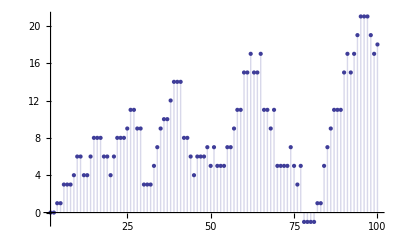

```mathematica
DiscretePlot[ M2[n,2],{n,2,100}]
```

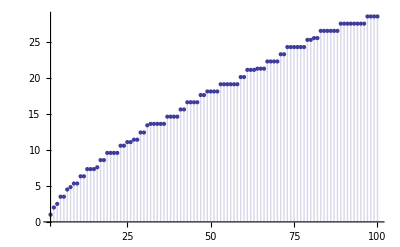

```mathematica
DiscretePlot[ (M1[n,-0.000001]-1)/0.000001,{n,2,100}]
```